## n States

### Infinitesimal matrix

```mathematica
Λ={{p*f1-p,p*f2,p*f3,p*f4},
{p*f1,p*f2-p,p*f3,p*f4},
{p*f1,p*f2,p*f3-p,p*f4},
{p*f1,p*f2,p*f3,p*f4-p}};
MatrixForm[Λ]
```

(-p+f1 p | f2 p | f3 p | f4 p
f1 p | -p+f2 p | f3 p | f4 p
f1 p | f2 p | -p+f3 p | f4 p
f1 p | f2 p | f3 p | -p+f4 p)

### Eigenvalues and Eigenvectors

```mathematica
eigvalues=Eigenvalues[Λ]
```

{-p,-p,-p,(-1+f1+f2+f3+f4) p}

```mathematica
eigvectors=Simplify[Eigenvectors[Λ]]
```

{{-f4/f1,0,0,1},{-f3/f1,0,1,0},{-f2/f1,1,0,0},{1,1,1,1}}

### Transition Matrix

```mathematica
A=MatrixExp[DiagonalMatrix[eigvalues]*s];
MatrixForm[A]
```

(ⅇ^(-p s) | 0 | 0 | 0
0 | ⅇ^(-p s) | 0 | 0
0 | 0 | ⅇ^(-p s) | 0
0 | 0 | 0 | ⅇ^((-1+f1+f2+f3+f4) p s))

```mathematica
B = Transpose[eigvectors];
MatrixForm[B]
```

(-f4/f1 | -f3/f1 | -f2/f1 | 1
0 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 1)

```mathematica
P=Dot[B,A,Inverse[B]]// Simplify;
MatrixForm[P]
```

((ⅇ^(-p s) (ⅇ^((f1+f2+f3+f4) p s) f1+f2+f3+f4))/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f2)/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f3)/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f4)/(f1+f2+f3+f4)
(ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f1)/(f1+f2+f3+f4) | (ⅇ^(-p s) (f1+ⅇ^((f1+f2+f3+f4) p s) f2+f3+f4))/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f3)/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f4)/(f1+f2+f3+f4)
(ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f1)/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f2)/(f1+f2+f3+f4) | (ⅇ^(-p s) (f1+f2+ⅇ^((f1+f2+f3+f4) p s) f3+f4))/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f4)/(f1+f2+f3+f4)
(ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f1)/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f2)/(f1+f2+f3+f4) | (ⅇ^(-p s) (-1+ⅇ^((f1+f2+f3+f4) p s)) f3)/(f1+f2+f3+f4) | (ⅇ^(-p s) (f1+f2+f3+ⅇ^((f1+f2+f3+f4) p s) f4))/(f1+f2+f3+f4))

## n States with Sum fi=1

### Infinitesimal matrix

```mathematica
f4=1-f1-f2-f3;
```

```mathematica
Λ={{p*f1-p,p*f2,p*f3,p*f4},
{p*f1,p*f2-p,p*f3,p*f4},
{p*f1,p*f2,p*f3-p,p*f4},
{p*f1,p*f2,p*f3,p*f4-p}};
MatrixForm[Λ]
```

(-p+f1 p | f2 p | f3 p | (1-f1-f2-f3) p
f1 p | -p+f2 p | f3 p | (1-f1-f2-f3) p
f1 p | f2 p | -p+f3 p | (1-f1-f2-f3) p
f1 p | f2 p | f3 p | -p+(1-f1-f2-f3) p)

### Eigenvalues and Eigenvectors

```mathematica
eigvalues=Eigenvalues[Λ]
```

{-p,-p,-p,0}

```mathematica
eigvectors=Simplify[Eigenvectors[Λ]]
```

{{(-1+f1+f2+f3)/f1,0,0,1},{-f3/f1,0,1,0},{-f2/f1,1,0,0},{1,1,1,1}}

### Transition Matrix

```mathematica
A=MatrixExp[DiagonalMatrix[eigvalues]*s];
MatrixForm[A]
```

(ⅇ^(-p s) | 0 | 0 | 0
0 | ⅇ^(-p s) | 0 | 0
0 | 0 | ⅇ^(-p s) | 0
0 | 0 | 0 | 1)

```mathematica
B = Transpose[eigvectors];
MatrixForm[B]
```

((-1+f1+f2+f3)/f1 | -f3/f1 | -f2/f1 | 1
0 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 1)

```mathematica
P=Dot[B,A,Inverse[B]]// Simplify;
MatrixForm[P]
```

(-ⅇ^(-p s) (-1+f1)+f1 | f2-ⅇ^(-p s) f2 | f3-ⅇ^(-p s) f3 | -ⅇ^(-p s) (-1+ⅇ^(p s)) (-1+f1+f2+f3)
f1-ⅇ^(-p s) f1 | -ⅇ^(-p s) (-1+f2)+f2 | f3-ⅇ^(-p s) f3 | -ⅇ^(-p s) (-1+ⅇ^(p s)) (-1+f1+f2+f3)
f1-ⅇ^(-p s) f1 | f2-ⅇ^(-p s) f2 | -ⅇ^(-p s) (-1+f3)+f3 | -ⅇ^(-p s) (-1+ⅇ^(p s)) (-1+f1+f2+f3)
f1-ⅇ^(-p s) f1 | f2-ⅇ^(-p s) f2 | f3-ⅇ^(-p s) f3 | ⅇ^(-p s) (f1+f2+f3-ⅇ^(p s) (-1+f1+f2+f3)))

```mathematica
-ⅇ^(-p s) (-1+ⅇ^(p s)) (-f4)
ⅇ^(-p s) (-1+ⅇ^(p s)) f4
 (-ⅇ^(-p s)+1) f4
-ⅇ^(-p s)f4+f4
```

```mathematica
ⅇ^(-p s) (1-f4)+f4
```

## Two States

### Infinitesimal matrix

```mathematica
Q={{-p12,p12},
{p21,-p21}};
MatrixForm[Q]
```

(-p12 | p12
p21 | -p21)

### Eigenvalues and Eigenvectors

```mathematica
Eigenvalues[Q]
```

{0,-p12-p21}

```mathematica
Simplify[Eigenvectors[Q]]
```

{{1,1},{-p12/p21,1}}

### Transition Matrix

```mathematica
Λ=MatrixExp[DiagonalMatrix[Eigenvalues[Q]*s]];
MatrixForm[A]
```

(1 | 0
0 | ⅇ^(-((p12+p21) s)))

```mathematica
V = Transpose[Simplify[Eigenvectors[Q]]];
MatrixForm[V]
```

(1 | -p12/p21
1 | 1)

```mathematica
P=Dot[V,Λ,Inverse[V]];
Simplify[MatrixForm[P]]
```

((ⅇ^(-((p12+p21) s)) p12+p21)/(p12+p21) | (p12-ⅇ^(-((p12+p21) s)) p12)/(p12+p21)
(p21-ⅇ^(-((p12+p21) s)) p21)/(p12+p21) | (p12+ⅇ^(-((p12+p21) s)) p21)/(p12+p21))

## ODE

```mathematica
pD=1/r;
p1=θ1/r^2+((θ2-θ1)*μ)/(r^2*(λ+μ+r));
ppi=(θ2-θ1)/(r^2*(λ+μ+r));
pis=μ/(μ+λ);
p0=-(γ*σ^2)/r^2;
β=(γ^2*σ^2)/(2*r)+ρ/r+Log[r]-1;
sigmapi[x_]=pD*σ+(ppi*S'[x])*h[x];
h[x_]=((θ2-θ1)/σ)*x*(1-x);
g[x_]:=-rγS(x)+f[x];
```

```mathematica
s=NDSolveValue[{-r*p0-r*S[x]+S'[x]*(pis-x)*(μ+λ)+1/2*S''[x]*h[x]^2-g'[x]*sigmapi*h[x]==r*γ*sigmapi[x]^2},S,{x,0,1}]
```

NDSolveValue::underdet: There are more dependent variables, {f[x],S[x]}, than equations, so the system is underdetermined.

NDSolveValue[{(γ σ^2)/r-r S[x]-(sigmapi (1-x) x (-θ1+θ2) (-rγS+f'[x]))/σ+(λ+μ) (-x+μ/(λ+μ)) S'[x]+((1-x)^2 x^2 (-θ1+θ2)^2 S''[x])/(2 σ^2)==r γ (σ/r+((1-x) x (-θ1+θ2)^2 S'[x])/(r^2 (r+λ+μ) σ))^2},S,{x,0,1}]

## ODE Tutorial

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
```

{{y→InterpolatingFunction[…]}}

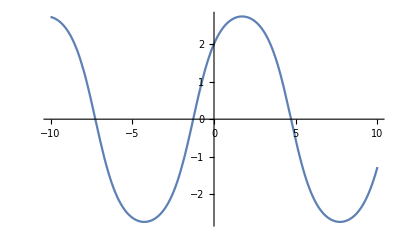

```mathematica
sol=NDSolve[ode1,y,{x,-10,10}]
Plot[y[x]/. sol,{x,-10,10}]
```